```mathematica
l0[x_] =((x - Pi/6)*(x - Pi/3)*(x - Pi/2))/((- Pi/6) * (-Pi/3) * (-Pi/2))
```

-(36 (-π/2+x) (-π/3+x) (-π/6+x))/π^3

```mathematica
l1[x_] = ((x - 0)*(x - Pi /3)*(x - Pi /2))/((Pi /6 )*(Pi /6 - Pi /3)*(Pi /6 - Pi /2))
```

(108 x (-π/2+x) (-π/3+x))/π^3

```mathematica
l2[x_] = ((x - 0)*(x - Pi /6)*(x - Pi /2))/((Pi /3)*(Pi /3 -Pi /6)*(Pi /3 - Pi /2))
```

-(108 x (-π/2+x) (-π/6+x))/π^3

```mathematica
l3[x_] = ((x )*(x - Pi /6)*(x - Pi /3))/((Pi /2)*(Pi /2 - Pi /6)*(Pi /2 - Pi /3))
```

(36 x (-π/3+x) (-π/6+x))/π^3

```mathematica
p[x_] = 0*l0[x] + (1/2)*l1[x] + (Sqrt[3]/2)*l2[x] + l3[x]
```

(54 x (-π/2+x) (-π/3+x))/π^3-(54 √3 x (-π/2+x) (-π/6+x))/π^3+(36 x (-π/3+x) (-π/6+x))/π^3

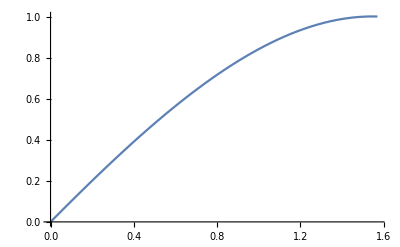

```mathematica
plotMain = Plot[p[x],{x, 0, Pi /2}]
```

```mathematica
f[x_] = Sin[x]
```

Sin[x]

```mathematica
g[x_] = Abs[f[x] - p[x]]
```

Abs[-(54 x (-π/2+x) (-π/3+x))/π^3+(54 √3 x (-π/2+x) (-π/6+x))/π^3-(36 x (-π/3+x) (-π/6+x))/π^3+Sin[x]]

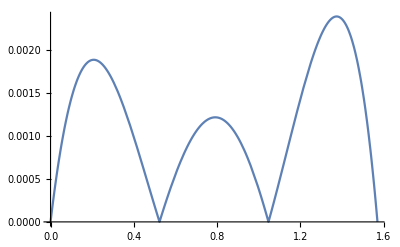

```mathematica
Plot[g[x], {x, 0, Pi /2}]
```

```mathematica
maxErr[x_] = 1/24*Abs[(x - 0)*(x - Pi/6)*(x - Pi /3)*(x - Pi /2)]
```

1/24 Abs[x (-π/2+x) (-π/3+x) (-π/6+x)]

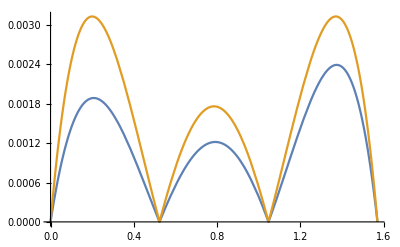

```mathematica
Plot[{g[x], maxErr[x]}, {x, 0, Pi /2}]
```

```mathematica
p[Pi /5]
```

2/5+(27 √3)/250